```mathematica
(*starting date: 04 May 2021*)
(*analytical model of Alfven wings when the background field has a flow-aligned component, B0=(B0x, 0, B0z), where B0x > 0 and B0z < 0*)
(*This model generates output in TWO different coordinate systems: (x,y,z) where z is antiparallel to B0, and (xcor, ycor=y, zcor), where xcor is along the incident flow direction*)
(*05/07/21: update: equations for magnetic field corrected*)
(*17 June 2021: Adjusted to Triton,*)

(*------------------------------------------------------------------*)
(*Basic Input Parameters*)
(*------------------------------------------------------------------*)
RE= 1353 * 10^3;(*moon radius in m*)
B0= 5.1369 * 10^-9; (*background field magnitude in T*)
theta= 42.94896* (2 π)/360; (*inclination angle in rd, as defined in Figure 3 of Neubauer1980, theta=0 means u0 perpendicular to B0. !TODO: Theta needs to become a free parameter!*)
B0x=0;
B0y=0;
B0z=-B0;  (*background magnetic field in system (x,y,z)*)
B0xcor=B0x Cos[theta]-B0z Sin[theta];
B0ycor=0;
B0zcor=B0x Sin[theta]+B0z Cos[theta]; (*background magnetic field in system (xcor,ycor,zcor)*)
n0=0.11 * 10^6; (*upstream number density in 1/m^3*)
u0=43*10^3; (*magnitude of upstream flow velocity in m/s*)
u0xcor=u0;
u0ycor=0;
u0zcor=0; (*upstream flow velocity in system (xcor,ycor,zcor)*)
u0x=u0 Cos[theta];
u0y=0;
u0z=-u0 Sin[theta];(*upstream flow velocity in system (x,y,z)*)
E0=u0*B0 *Cos[theta]; (*MAGNITUDE OF convective electric field*)
E0norm= u0*B0; (*may be needed for normalization purposes*)
mp=1.6726231*10^-27; (*proton mass*)
m=7.5 * mp; (*upstream ion mass*)
mu0= 4 * 3.14159265359* 10^-7; (*magnetic permeability of vacuum*)

(*------------------------------------------------------------------*)
(*Derived parameters for Alfven wings*)
(*------------------------------------------------------------------*)
vA=B0/(√(mu0 * n0 * m)); (*Alfven velocity*)
MA= u0/vA (*Alfvenic Mach number*)
SigmaAn=1/(mu0 * vA*√(1+MA^2-2*MA* Sin[theta])); (*Alfven conductance, northern wing*)
SigmaAs=1/(mu0 * vA*√(1+MA^2+2*MA* Sin[theta]));(*Alfven conductance, southern wing*)
ThetaN=ArcTan[(MA Cos[theta])/(1-MA Sin[theta])] *360/(2 π)(*inclination angle against B0 for NORTHERN Alfven wing*)
ThetaS=ArcTan[(MA Cos[theta])/(1+MA Sin[theta])] *360/(2 π)(*inclination angle against B0 for NORTHERN Alfven wing*)
SinThetaN=(MA Cos[theta])/(√(1+MA^2-2*MA* Sin[theta]));
CosThetaN=(1-MA Sin[theta])/(√(1+MA^2-2*MA* Sin[theta]));
SinThetaS=(MA Cos[theta])/(√(1+MA^2+2*MA* Sin[theta]));
CosThetaS=(1+MA Sin[theta])/(√(1+MA^2+2*MA* Sin[theta]));
```

0.348577

18.5011

11.6498

```mathematica
(*------------------------------------------------------------------*)
(*Ionosphere model, mostly taken from Simon2021 analytical model, in coordinates (x,y,z)*)
(*Important: need SAME conductance profile in both hemispheres, otherwise boundary condition from Saur2007 needs to be applied*)
(*------------------------------------------------------------------*)
```

```mathematica
SigmaP= 500;(*exospheric Pedersen conductance, called SigmaP0 in the 2021 paper, STILL SAME SIGMAP0 IN BOTH HEMISPHERES*)
H= 70 * 10^3; (*exospheric scale height, from Arnold2020b*)
r[x_,y_] = √(x^2+ y^2); (*radial distance from z axis in cylindrical coordinates, NOT radial distance to Europa's surface, measured perpendicular to the background magnetic field or z axis, (x,y) dependence NOT needed for merely plotting the exospheric conductance profile*)
R1= RE ;(*radial boundary of the Europa fluxtube, x^2+y^2 = RE^2*)
R2=  RE+ 5 H;(*outer boundary of region with non-zero transverse conductance, assumming the atmosphere "ends" at a distance of 5 scale heights. exp(-5)=0.00674*)
betaN = 1/(3H) ; (*NEW 05/2021: north only*)
betaS=1/R1 Log[((SigmaP+SigmaAn)Exp[betaN*R1]+(SigmaAs-SigmaAn))/(SigmaP+SigmaAs)];
(*given input parameter for conductance profile, using some multiple of the exospheric scale height H here, NEW; BETA IS DIFFERENT FOR NORTHERN AND SOUTHERN HEMISPHERES*)
Sigma1n[r_]= (SigmaP+SigmaAn)* Exp[betaN* r]-SigmaAn; 
Sigma1s[r_]= (SigmaP+SigmaAs)* Exp[betaS* r]-SigmaAs;(*Pedersen conductance within the Europa fluxtube r < R1, 05/2021: NOW DIFFERENT FOR NORTH AND SOUTH!!*)
deltaN=(Log[(SigmaP+SigmaAn)/SigmaAn]+ betaN * R1)/(R2-R1);
deltaS=Log[(SigmaAn Exp[deltaN*(R2-R1)]+SigmaAs-SigmaAn)/SigmaAs]/(R2-R1);
Sigma2n[r_]= SigmaAn *Exp[deltaN*(R2-r)]-SigmaAn;

Sigma2s[r_]= SigmaAs *Exp[deltaS*(R2-r)]-SigmaAs;
(*Pedersen conductance outside the Europa fluxtube, but within the exosphere R1 < r < R2,NEW 05/2021: NOW DIFFERENT FOR NORTH AND SOUTH!!*)
Sigma3[r_]= 0 ; (*Pedersen conductance outside of Europa fluxtube, R2 < r, always the same in both hemispheres, no N/S splitting required*)
SigmaExon[r_]= Piecewise[{{Sigma1n[r], r ≤ R1},{Sigma2n[r], R1 < r ≤ R2},{Sigma3[r], R2 < r}}];
SigmaExos[r_]= Piecewise[{{Sigma1s[r], r ≤ R1},{Sigma2s[r], R1 < r ≤ R2},{Sigma3[r], R2 < r}}];
(*putting all three segments together, 05/2021: NOW DIFFERENT EQUATIONS FOR NORTH AND SOUTH BUT PROFILES SHOULD STILL LOOK N E A R L Y identical in regions 1 and 2!!*)
```

45475.7

45190.2

1.00632

0.999647

0.999774

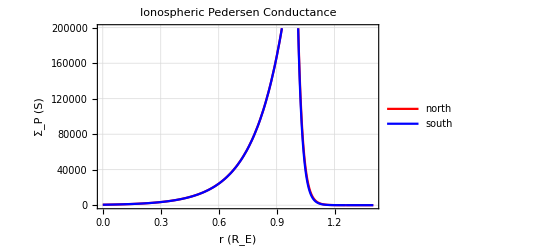

```mathematica
(*------------------------------------------------------------------*)
(*Ionosphere model, plots and derived parameters*)
(*------------------------------------------------------------------*)
AvSigmaPn= 1/R2 ∫_0^R2 SigmaExon[r]ⅆr (*average Pedersen conductivity, northern hemisphere*)
AvSigmaPs= 1/R2 ∫_0^R2 SigmaExos[r]ⅆr (*average Pedersen conductivity, southern hemisphere*)
AvSigmaPn/AvSigmaPs (*should be as close as possible to 1*)
alphaN=AvSigmaPn/(AvSigmaPn+2*SigmaAn) (*average interaction strength, north !this is only an estimation!*)
alphaS=AvSigmaPs/(AvSigmaPs+2*SigmaAs) (*average interaction strength, north !this is only an estimation!*)
Plot[{SigmaExon[r*RE],SigmaExos[r*RE]},{r,0,1.4}, FrameLabel->{"r (R_E)","Σ_P (S)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Ionospheric Pedersen Conductance", PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends ->{"north", "south"}]
```

```mathematica
(*-------------------------------------------------------------------------------*)
(*05 May 2021: Potentials, magnetic field and flow velocity, all in system (x,y,z)*)
(*-------------------------------------------------------------------------------*)
(*linear system, northern wing*)
Mn={{(betaN*R1-1+Exp[-betaN* R1])/R1,(deltaN*R1+1)/R1, (-Exp[deltaN*R1])/R1,0},{0, -(deltaN*R2+1)/R2, Exp[deltaN*R2]/R2,-1/R2},{(1-(betaN*R1+1)*Exp[-betaN*R1])/R1^2,-1/R1^2, -1/R1^2 Exp[deltaN*R1] (deltaN*R1-1) ,0},{0,1/R2^2,(Exp[deltaN*R2] *(deltaN*R2-1))/R2^2, 1/R2^2}};
c={{0},{E0*R2},{0},{E0}};
MatrixForm[Mn];
{{K1n},{K3n},{K4n},{K5n}}=Inverse[Mn].c;
(*linear system, southern wing*)
Ms={{(betaS*R1-1+Exp[-betaS* R1])/R1,(deltaS*R1+1)/R1, (-Exp[deltaS*R1])/R1,0},{0, -(deltaS*R2+1)/R2, Exp[deltaS*R2]/R2,-1/R2},{(1-(betaS*R1+1)*Exp[-betaS*R1])/R1^2,-1/R1^2, -1/R1^2 Exp[deltaS*R1] (deltaS*R1-1) ,0},{0,1/R2^2,(Exp[deltaS*R2] *(deltaS*R2-1))/R2^2, 1/R2^2}};
(*same c vector as for northern wing*)
MatrixForm[Ms];
{{K1s},{K3s},{K4s},{K5s}}=Inverse[Ms].c;
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.02398×10^-6,0.0000309993,-4.46292×10^11,0.},{0.,-«20»,«23»,-5.87199×10^-7},{«1»},{0.,3.44803×10^-13,4.18514×10^11,3.44803×10^-13}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.02823×10^-6,0.0000322907,-2.56121×10^12,0.},{0.,-«24»,«22»,-5.87199×10^-7},{«1»},{0.,3.44803×10^-13,3.93852×10^12,3.44803×10^-13}} may contain significant numerical errors.

```mathematica
(*Potentials, their derivatives, magnetic field, and bulk velocity*)
sinphi[x_,y_]=y/(√(x^2+y^2));
cosphi[x_,y_]=x/(√(x^2+y^2));
(*potential psi, northern wing*)
psi1n[x_,y_]=sinphi[x,y]* 1/r[x,y](K1n*(betaN*r[x,y]-1)+K1n*Exp[-betaN*r[x,y]]);
psi2n[x_,y_]=sinphi[x,y]*1/r[x,y](-K3n*(deltaN*r[x,y]+1)+K4n*Exp[deltaN*r[x,y]]);
psi3n[x_,y_]=sinphi[x,y]*(E0*r[x,y]+K5n/r[x,y]);
psin[x_,y_]=Piecewise[{{0,r[x,y]==0},{psi1n[x,y],0<r[x,y] ≤ R1},{psi2n[x,y],  R1 < r[x,y] ≤ R2},{psi3n[x,y], R2< r[x,y] }}];
(*potential psi, southern wing*)
psi1s[x_,y_]=sinphi[x,y]* 1/r[x,y](K1s*(betaS*r[x,y]-1)+K1s*Exp[-betaS*r[x,y]]);
psi2s[x_,y_]=sinphi[x,y]*1/r[x,y](-K3s*(deltaS*r[x,y]+1)+K4s*Exp[deltaS*r[x,y]]);
psi3s[x_,y_]=sinphi[x,y]*(E0*r[x,y]+K5s/r[x,y]);
psis[x_,y_]=Piecewise[{{0,r[x,y]==0},{psi1s[x,y],0<r[x,y] ≤ R1},{psi2s[x,y],  R1 < r[x,y] ≤ R2},{psi3s[x,y], R2< r[x,y] }}];
(*derivatives of psi, magnetic field, and flow pattern u within the Alfven wings*)
(*derivatives, northern wing*)
dxpsi1n[x_,y_]= cosphi[x,y]*sinphi[x,y]*K1n*((1-Exp[-betaN*r[x,y]]*(betaN*r[x,y]+1))/(r[x,y]*r[x,y]))- sinphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](K1n*(betaN*r[x,y]-1)+K1n*Exp[-betaN*r[x,y]]);
dxpsi2n[x_,y_]=cosphi[x,y]*sinphi[x,y]*((K3n+K4n*Exp[deltaN*r[x,y]]*(deltaN*r[x,y]-1))/(r[x,y]*r[x,y]))- sinphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](-K3n*(deltaN*r[x,y]+1)+K4n*Exp[deltaN*r[x,y]]);
dxpsi3n[x_,y_]=cosphi[x,y]*sinphi[x,y]*(E0-K5n/(r[x,y]*r[x,y]))- sinphi[x,y]/r[x,y]*cosphi[x,y]*(E0*r[x,y]+K5n/r[x,y]);
dypsi1n[x_,y_]=sinphi[x,y]*sinphi[x,y]*K1n*((1-Exp[-betaN*r[x,y]]*(betaN*r[x,y]+1))/(r[x,y]*r[x,y]))+ cosphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](K1n*(betaN*r[x,y]-1)+K1n*Exp[-betaN*r[x,y]]);
dypsi2n[x_,y_]=sinphi[x,y]*sinphi[x,y]*((K3n+K4n*Exp[deltaN*r[x,y]]*(deltaN*r[x,y]-1))/(r[x,y]*r[x,y]))+ cosphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](-K3n*(deltaN*r[x,y]+1)+K4n*Exp[deltaN*r[x,y]]);
dypsi3n[x_,y_]=sinphi[x,y]*sinphi[x,y]*(E0-K5n/(r[x,y]*r[x,y]))+ cosphi[x,y]/r[x,y]*cosphi[x,y]*(E0*r[x,y]+K5n/r[x,y]);
dxpsin[x_,y_]=Piecewise[{{0,r[x,y]==0},{dxpsi1n[x,y],0<r[x,y] ≤ R1},{dxpsi2n[x,y],  R1 < r[x,y] ≤ R2},{dxpsi3n[x,y], R2< r[x,y] }}];
dypsin[x_,y_]=Piecewise[{{K1n *betaN^2/2,r[x,y]==0},{dypsi1n[x,y],0<r[x,y] ≤ R1},{dypsi2n[x,y],  R1 < r[x,y] ≤ R2},{dypsi3n[x,y], R2< r[x,y] }}];
(*derivaties, southern wing*)
dxpsi1s[x_,y_]= cosphi[x,y]*sinphi[x,y]*K1s*((1-Exp[-betaS*r[x,y]]*(betaS*r[x,y]+1))/(r[x,y]*r[x,y]))- sinphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](K1s*(betaS*r[x,y]-1)+K1s*Exp[-betaS*r[x,y]]);
dxpsi2s[x_,y_]=cosphi[x,y]*sinphi[x,y]*((K3s+K4s*Exp[deltaS*r[x,y]]*(deltaS*r[x,y]-1))/(r[x,y]*r[x,y]))- sinphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](-K3s*(deltaS*r[x,y]+1)+K4s*Exp[deltaS*r[x,y]]);
dxpsi3s[x_,y_]=cosphi[x,y]*sinphi[x,y]*(E0-K5s/(r[x,y]*r[x,y]))- sinphi[x,y]/r[x,y]*cosphi[x,y]*(E0*r[x,y]+K5s/r[x,y]);
dypsi1s[x_,y_]=sinphi[x,y]*sinphi[x,y]*K1s*((1-Exp[-betaS*r[x,y]]*(betaS*r[x,y]+1))/(r[x,y]*r[x,y]))+ cosphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](K1s*(betaS*r[x,y]-1)+K1s*Exp[-betaS*r[x,y]]);
dypsi2s[x_,y_]=sinphi[x,y]*sinphi[x,y]*((K3s+K4s*Exp[deltaS*r[x,y]]*(deltaS*r[x,y]-1))/(r[x,y]*r[x,y]))+ cosphi[x,y]/r[x,y]*cosphi[x,y]*1/r[x,y](-K3s*(deltaS*r[x,y]+1)+K4s*Exp[deltaS*r[x,y]]);
dypsi3s[x_,y_]=sinphi[x,y]*sinphi[x,y]*(E0-K5s/(r[x,y]*r[x,y]))+ cosphi[x,y]/r[x,y]*cosphi[x,y]*(E0*r[x,y]+K5s/r[x,y]);
dxpsis[x_,y_]=Piecewise[{{0,r[x,y]==0},{dxpsi1s[x,y],0<r[x,y] ≤ R1},{dxpsi2s[x,y],  R1 < r[x,y] ≤ R2},{dxpsi3s[x,y], R2< r[x,y] }}];
dypsis[x_,y_]=Piecewise[{{K1s *betaS^2/2,r[x,y]==0},{dypsi1s[x,y],0<r[x,y] ≤ R1},{dypsi2s[x,y],  R1 < r[x,y] ≤ R2},{dypsi3s[x,y], R2< r[x,y] }}];
(*magnetic field, northern wing*) 
Bxnorth[x_,y_]= -SinThetaN* √(B0^2- mu0^2*SigmaAn^2*((CosThetaN)^2(dxpsin[x,y])^2 +(dypsin[x,y])^2))+ mu0*SigmaAn*CosThetaN* dypsin[x,y] ;
Bynorth[x_,y_]=-CosThetaN* mu0*SigmaAn* dxpsin[x,y];
Bznorth[x_,y_]=-CosThetaN*√(B0^2- mu0^2*SigmaAn^2*((CosThetaN)^2(dxpsin[x,y])^2 +(dypsin[x,y])^2))- mu0*SigmaAn*SinThetaN*dypsin[x,y] ;
(*magnetic field, southern wing*)
Bxsouth[x_,y_]= SinThetaS* √(B0^2- mu0^2*SigmaAs^2*((CosThetaS)^2 (dxpsis[x,y])^2 +(dypsis[x,y])^2))- mu0*SigmaAs*CosThetaS*dypsis[x,y] ;
Bysouth[x_,y_]=CosThetaS* mu0*SigmaAs* dxpsis[x,y];
Bzsouth[x_,y_]=-CosThetaS*√(B0^2- mu0^2*SigmaAs^2*((CosThetaS)^2(dxpsis[x,y])^2 +(dypsis[x,y])^2))- SinThetaS*mu0*SigmaAs*dypsis[x,y] ;
(*velocity field, northern wing*)
uxnorth[x_,y_]= u0x+ (Bxnorth[x,y]-B0x)/(√(mu0 * n0 * m));
uynorth[x_,y_] = u0y+(Bynorth[x,y]-B0y)/(√(mu0 * n0 * m));
uznorth[x_,y_]= u0z+ (Bznorth[x,y]-B0z)/(√(mu0 * n0 * m)); 
(*velocity field, southern wing*)
uxsouth[x_,y_]= u0x - (Bxsouth[x,y]-B0x)/(√(mu0 * n0 * m));
uysouth[x_,y_] = u0y-(Bysouth[x,y]-B0y)/(√(mu0 * n0 * m));
uzsouth[x_,y_]= u0z- (Bzsouth[x,y]-B0z)/(√(mu0 * n0 * m));
```

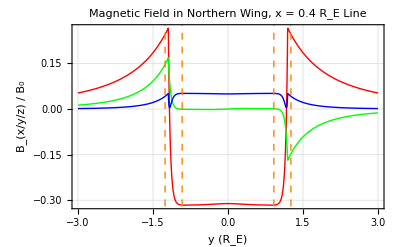

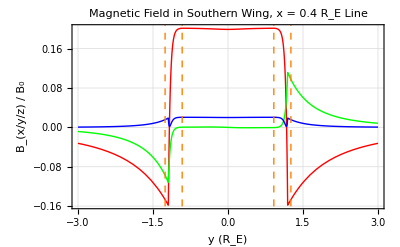

```mathematica
(*------------------------------------------------------------------------------------*)
(*a few plots from Simon2021, to make sure that this all works*)
(*------------------------------------------------------------------------------------*)
(*magnetic field, see figure 6 from Simon2021 northern and southern wing should be somewhat different now*)
Plotmagnorth=Plot[{Bxnorth[0.4RE,y*RE]/(B0),Bynorth[0.4 RE,y*RE]/(B0),Bznorth[0.4 RE,y*RE]/(B0)+B0/B0},{y,-3,3}, FrameLabel->{"y (R_E)","B_(x/y/z) / B_0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Magnetic Field in Northern Wing, x = 0.4 R_E Line", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}}, Epilog->{Directive[Dashed, Orange],InfiniteLine[{{-0.9165,-0.3},{-0.9165,0.3}}],InfiniteLine[{{0.9165,-0.3},{0.9165,0.3}}],InfiniteLine[{{1.258,-0.3},{1.258,0.3}}],InfiniteLine[{{-1.258,-0.3},{-1.258,0.3}}]} (*,PlotLegends ->{"B_x","B_y","B_z"}*)] 
Plotmagsouth=Plot[{Bxsouth[0.4RE,y*RE]/(B0),Bysouth[0.4 RE,y*RE]/(B0),Bzsouth[0.4 RE,y*RE]/(B0)+B0/B0},{y,-3,3}, FrameLabel->{"y (R_E)","B_(x/y/z) / B_0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Magnetic Field in Southern Wing, x = 0.4 R_E Line", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}},Epilog->{Directive[Dashed, Orange],InfiniteLine[{{-0.9165,-0.3},{-0.9165,0.3}}],InfiniteLine[{{0.9165,-0.3},{0.9165,0.3}}],InfiniteLine[{{1.258,-0.3},{1.258,0.3}}],InfiniteLine[{{-1.258,-0.3},{-1.258,0.3}}]}(*,PlotLegends ->{"B_x","B_y","B_z"}*)]
```

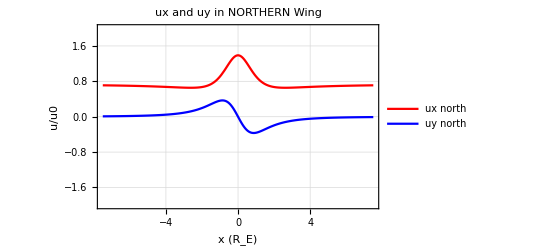

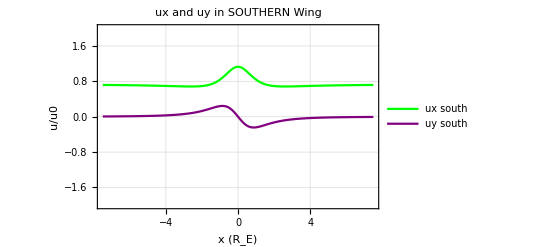

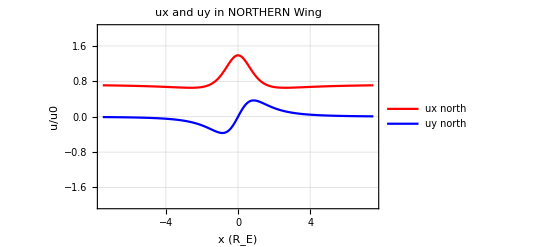

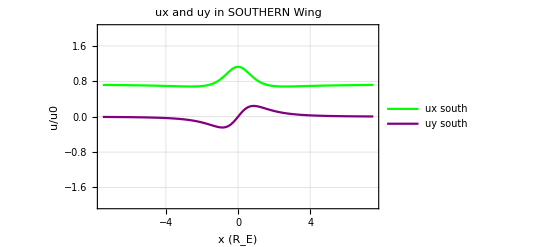

```mathematica
(*velocity field, figure 2 of Simon2021*)
uxnorthshiftpos[x_]=uxnorth[x,1.5RE]/u0;(*cut at y=1.5 RE, i.e., displaced TOWARD Jupiter*)
uynorthshiftpos[x_]=uynorth[x,1.5RE]/u0;
uxsouthshiftpos[x_]=uxsouth[x,1.5RE]/u0;
uysouthshiftpos[x_]=uysouth[x,1.5RE]/u0;
Plot[{uxnorthshiftpos[x*RE],uynorthshiftpos[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in NORTHERN Wing", PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends ->{"ux north","uy north"},PlotRange->{-2,2}]
Plot[{uxsouthshiftpos[x*RE],uysouthshiftpos[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in SOUTHERN Wing", PlotStyle->{{Green,Thick},{Purple,Thick}},PlotLegends ->{"ux south","uy south"},PlotRange->{-2,2}]
uxnorthshiftneg[x_]=uxnorth[x,-1.5RE]/u0; (*cut at y=-1.5 RE, i.e., displaced AWAY FROM Jupiter*)
uynorthshiftneg[x_]=uynorth[x,-1.5RE]/u0;
uxsouthshiftneg[x_]=uxsouth[x,-1.5RE]/u0;
uysouthshiftneg[x_]=uysouth[x,-1.5RE]/u0;
Plot[{uxnorthshiftneg[x*RE],uynorthshiftneg[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in NORTHERN Wing", PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends ->{"ux north","uy north"},PlotRange->{-2,2}]
Plot[{uxsouthshiftneg[x*RE],uysouthshiftneg[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in SOUTHERN Wing", PlotStyle->{{Green,Thick},{Purple,Thick}},PlotLegends ->{"ux south","uy south"},PlotRange->{-2,2}]
```

```mathematica
(*-----------------------------------------------------------------------------------*)
(*so far, everything is given in coordinate system (x,y,z) where z is antiparallel to the background field. Now we need to transform into system (xcor,ycor,zcor) where xcor is along the coritation direction*)
(*-----------------------------------------------------------------------------------*)
(*position vectors*)
x[xcor_,ycor_,zcor_]= xcor* Cos[theta]+zcor*Sin[theta];
y[xcor_,ycor_,zcor_]= ycor;
z[xcor_,ycor_,zcor_]= -xcor* Sin[theta]+zcor*Cos[theta]; (*z is actually not even needed, since in the (x,y,z) system the solution is constant in z direction, i.e., there are no z dependencies in any quantity*)
(*magnetic field components in northern wing*)
Bxnorthcor[xcor_,ycor_,zcor_]=Bxnorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta]- Bznorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta];
Bynorthcor[xcor_,ycor_,zcor_]= Bynorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]];
Bznorthcor[xcor_,ycor_,zcor_]= Bxnorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta]+ Bznorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta];
(*magnetic field components in southern wing*)
Bxsouthcor[xcor_,ycor_,zcor_]=Bxsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta]- Bzsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta];
Bysouthcor[xcor_,ycor_,zcor_]= Bysouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]];
Bzsouthcor[xcor_,ycor_,zcor_]= Bxsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta]+ Bzsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta];
(*bulk velocity in northern wing*)
uxnorthcor[xcor_,ycor_,zcor_]=uxnorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta]- uznorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta];
uynorthcor[xcor_,ycor_,zcor_]= uynorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]];
uznorthcor[xcor_,ycor_,zcor_]= uxnorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta]+ uznorth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta];
(*bulk velocity in southern wing*)
uxsouthcor[xcor_,ycor_,zcor_]=uxsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta]- uzsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta];
uysouthcor[xcor_,ycor_,zcor_]= uysouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]];
uzsouthcor[xcor_,ycor_,zcor_]= uxsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Sin[theta]+ uzsouth[x[xcor,ycor,zcor],y[xcor,ycor,zcor]]*Cos[theta];
```

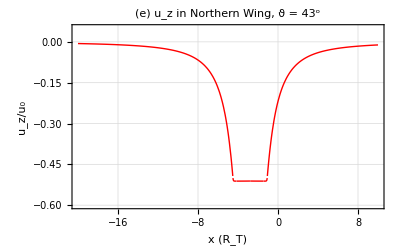

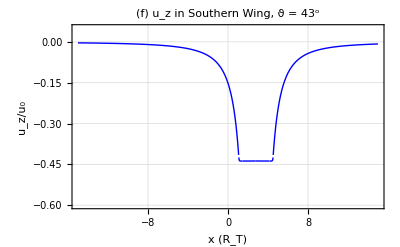

uz_north43.pdf

uz_south43.pdf

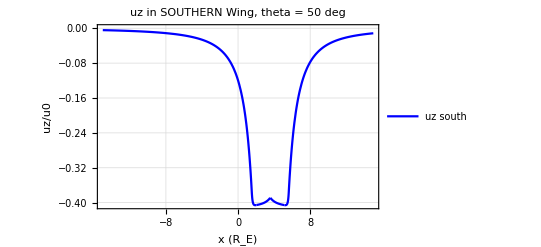

```mathematica
(*---------------------------------------------------------------------------*)
(*now: plotting the results in system (xcor,ycor, zcor)*)
(*---------------------------------------------------------------------------*)
Plot1=Plot[uznorthcor[xcor*RE,0, 3*RE]/u0,{xcor,-20,10},FrameLabel->{"x (R_T)","u_z/u_0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(e) u_z in Northern Wing, ϑ = 43^o", PlotStyle->{{Red,Thick}} (*,PlotLegends ->{"uz north"}*),PlotRange->{-0.6,0.05}]
Plot2=Plot[uzsouthcor[xcor*RE,0, -3*RE]/u0,{xcor,-15,15},FrameLabel->{"x (R_T)","u_z/u_0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(f) u_z in Southern Wing, ϑ = 43^o", PlotStyle->{{Blue,Thick}}, PlotRange->{-0.6,0.05}(*,PlotLegends ->{"uz south"}*)]
Export["uz_north43.pdf",Plot1]
Export["uz_south43.pdf",Plot2]
```